```mathematica
(*Mathematica*)
```

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Transpose[CompanionMatrix[-x^10-2*x^9+3*x^8-4*x^7-4*x^6-5*x^5+5*x^4-3*x^3+3*x^2-x+1,x] ]
```

{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{1,-1,3,-3,5,-5,-4,-4,3,-2}}

```mathematica
(*Riley slice as Orthogonal Teichmuller space of two bridge knots:3_1,4_1,5_2,6_1,6_2,7_4,7_7,8_11,...*)
```

```mathematica
Clear[p]
```

```mathematica
p[x_,0]=x-1;
p[x_,1]=(x^2-x+1);
p[x_,2]=x^3+x^2+2*x+1;
p[x_,3]=x^4-x^3+3*x^2-2*x+1;
p[x_,4]=x^5-x^4+x^3-2*x^2+x-1;
p[x_,5]=x^3+2*x-1;
p[x_,6]=x^4+x^2-x+1;
p[x_,7]=x^10-2*x^9+3*x^8-4*x^7-4*x^6-5*x^5+5*x^4-3*x^3+3*x^2-x+1;
```

```mathematica
mp=Table[Transpose[CompanionMatrix[p[x,i],x] ],{i,1,7}]
```

{{{0,1},{-1,1}},{{0,1,0},{0,0,1},{-1,-2,-1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1,2,-3,1}},{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,-1,2,-1,1}},{{0,1,0},{0,0,1},{1,-2,0}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1,1,-1,0}},{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{-1,1,-3,3,-5,5,4,4,-3,2}}}

```mathematica
Table[N[Eigenvalues[mp[[i]]]],{i,7}]
```

{{0.5+0.866025 ⅈ,0.5-0.866025 ⅈ},{-0.21508+1.30714 ⅈ,-0.21508-1.30714 ⅈ,-0.56984},{0.104877+1.55249 ⅈ,0.104877-1.55249 ⅈ,0.395123+0.506844 ⅈ,0.395123-0.506844 ⅈ},{1.30408,-0.42855+1.03928 ⅈ,-0.42855-1.03928 ⅈ,0.276511+0.728237 ⅈ,0.276511-0.728237 ⅈ},{-0.226699+1.46771 ⅈ,-0.226699-1.46771 ⅈ,0.453398},{-0.547424+1.12087 ⅈ,-0.547424-1.12087 ⅈ,0.547424+0.585652 ⅈ,0.547424-0.585652 ⅈ},{2.08295,0.405506+1.86405 ⅈ,0.405506-1.86405 ⅈ,-0.889639+0.653912 ⅈ,-0.889639-0.653912 ⅈ,0.752897,-0.21581+0.586619 ⅈ,-0.21581-0.586619 ⅈ,0.28202+0.536993 ⅈ,0.28202-0.536993 ⅈ}}

```mathematica
a=Table[x/.NSolve[p[x,i]==0,x],{i,0,7}]
```

{{1.},{0.5-0.866025 ⅈ,0.5+0.866025 ⅈ},{-0.56984,-0.21508-1.30714 ⅈ,-0.21508+1.30714 ⅈ},{0.104877-1.55249 ⅈ,0.104877+1.55249 ⅈ,0.395123-0.506844 ⅈ,0.395123+0.506844 ⅈ},{-0.42855-1.03928 ⅈ,-0.42855+1.03928 ⅈ,0.276511-0.728237 ⅈ,0.276511+0.728237 ⅈ,1.30408},{-0.226699-1.46771 ⅈ,-0.226699+1.46771 ⅈ,0.453398},{-0.547424-1.12087 ⅈ,-0.547424+1.12087 ⅈ,0.547424-0.585652 ⅈ,0.547424+0.585652 ⅈ},{-0.889639-0.653912 ⅈ,-0.889639+0.653912 ⅈ,-0.21581-0.586619 ⅈ,-0.21581+0.586619 ⅈ,0.28202-0.536993 ⅈ,0.28202+0.536993 ⅈ,0.405506-1.86405 ⅈ,0.405506+1.86405 ⅈ,0.752897,2.08295}}

```mathematica
Abs[a]
```

{{1.},{1.,1.},{0.56984,1.32472,1.32472},{1.55603,1.55603,0.642661,0.642661},{1.12417,1.12417,0.778965,0.778965,1.30408},{1.48512,1.48512,0.453398},{1.24741,1.24741,0.801661,0.801661},{1.10411,1.10411,0.625057,0.625057,0.606545,0.606545,1.90765,1.90765,0.752897,2.08295}}

```mathematica
(*unitary conversion polynomials: q polynomials*)
```

```mathematica
q=Table[ExpandAll[Product[x-a[[i,j]]/Norm[a[[i,j]]],{j,Length[a[[i]]]}]]//Chop,{i,Length[a]}]
```

{-1.+x,1.-1. x+x^2,1.+1.32472 x+1.32472 x^2+x^3,1.-1.36445 x+2.16576 x^2-1.36445 x^3+x^4,-1.+0.947513 x-1.40623 x^2+1.40623 x^3-0.947513 x^4+x^5,-1.+0.694706 x-0.694706 x^2+x^3,1.-0.488026 x+0.801309 x^2-0.488026 x^3+x^4,1.-1.05303 x+1.49479 x^2-1.58739 x^3+1.11992 x^4-1.9486 x^5+1.11992 x^6-1.58739 x^7+1.49479 x^8-1.05303 x^9+x^10}

```mathematica
Table[x/.NSolve[q[[i]]==0,x],{i,8}]
```

{{1.},{0.5-0.866025 ⅈ,0.5+0.866025 ⅈ},{-1.,-0.162359-0.986732 ⅈ,-0.162359+0.986732 ⅈ},{0.0674001-0.997726 ⅈ,0.0674001+0.997726 ⅈ,0.614824-0.788664 ⅈ,0.614824+0.788664 ⅈ},{-0.381216-0.924486 ⅈ,-0.381216+0.924486 ⅈ,0.354972-0.934877 ⅈ,0.354972+0.934877 ⅈ,1.},{-0.152647-0.988281 ⅈ,-0.152647+0.988281 ⅈ,1.},{-0.438849-0.898561 ⅈ,-0.438849+0.898561 ⅈ,0.682862-0.730548 ⅈ,0.682862+0.730548 ⅈ},{-0.805752-0.592253 ⅈ,-0.805752+0.592253 ⅈ,-0.345265+0.938505 ⅈ,-0.345265-0.938505 ⅈ,0.212569-0.977146 ⅈ,0.212569+0.977146 ⅈ,0.464961+0.885331 ⅈ,0.464961-0.885331 ⅈ,1.,1.}}

```mathematica
(* conversion unitary polynomial matrices *)
```

```mathematica
mc=Table[Transpose[CompanionMatrix[q[[i]],x] ],{i,2,8}]
```

{{{0,1},{-1.,1.}},{{0,1,0},{0,0,1},{-1.,-1.32472,-1.32472}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1.,1.36445,-2.16576,1.36445}},{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1.,-0.947513,1.40623,-1.40623,0.947513}},{{0,1,0},{0,0,1},{1.,-0.694706,0.694706}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1.,0.488026,-0.801309,0.488026}},{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{-1.,1.05303,-1.49479,1.58739,-1.11992,1.9486,-1.11992,1.58739,-1.49479,1.05303}}}

```mathematica
Table[N[Eigenvalues[mc[[i]]]],{i,7}]
```

{{0.5+0.866025 ⅈ,0.5-0.866025 ⅈ},{-1.+0. ⅈ,-0.162359+0.986732 ⅈ,-0.162359-0.986732 ⅈ},{0.0674001+0.997726 ⅈ,0.0674001-0.997726 ⅈ,0.614824+0.788664 ⅈ,0.614824-0.788664 ⅈ},{1.+0. ⅈ,0.354972+0.934877 ⅈ,0.354972-0.934877 ⅈ,-0.381216+0.924486 ⅈ,-0.381216-0.924486 ⅈ},{-0.152647+0.988281 ⅈ,-0.152647-0.988281 ⅈ,1.+0. ⅈ},{-0.438849+0.898561 ⅈ,-0.438849-0.898561 ⅈ,0.682862+0.730548 ⅈ,0.682862-0.730548 ⅈ},{0.212569+0.977146 ⅈ,0.212569-0.977146 ⅈ,1.+3.40597×10^-9 ⅈ,1.-3.40597×10^-9 ⅈ,-0.805752+0.592253 ⅈ,-0.805752-0.592253 ⅈ,-0.345265+0.938505 ⅈ,-0.345265-0.938505 ⅈ,0.464961+0.885331 ⅈ,0.464961-0.885331 ⅈ}}

```mathematica
Abs[%]
```

{{1.,1.},{1.,1.,1.},{1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.},{1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
(*mp.mt=mc: mt=mp^(-1).mc*)
```

```mathematica
mt=Table[Inverse[mp[[i]]].mc[[i]],{i,7}]
```

{{{1.,0.},{0.,1.}},{{1.,-0.675282,0.324718},{0.,1.,0.},{0.,0.,1.}},{{1.,0.635552,-0.834243,-0.364448},{0.,1.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.}},{{1.,0.0524871,-0.593771,-0.406229,-0.0524871},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.},{0.,0.,0.,0.,1.}},{{1.,1.30529,0.694706},{0.,1.,0.},{0.,0.,1.}},{{1.,0.511974,-0.198691,-0.488026},{0.,1.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.}},{{1.,-0.0530255,-1.50521,1.41261,-3.88008,3.0514,5.11992,2.41261,-1.50521,0.946975},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}}}

```mathematica
Table[N[Eigenvalues[mt[[i]]]],{i,7}]
```

{{1.,1.},{1.,1.,1.},{1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.},{1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
(*all the inversion matrix polynomial as Pascal (x-1)^n types*)
```

```mathematica
Table[CharacteristicPolynomial[Inverse[mp[[i]]].mc[[i]],x],{i,7}]
```

{1.-2. x+x^2,1.-3. x+3. x^2-x^3,1.-4. x+6. x^2-4. x^3+x^4,1.-5. x+10. x^2-10. x^3+5. x^4-x^5,1.-3. x+3. x^2-x^3,1.-4. x+6. x^2-4. x^3+x^4,1.-10. x+45. x^2-120. x^3+210. x^4-252. x^5+210. x^6-120. x^7+45. x^8-10. x^9+x^10}

```mathematica
b=Table[Min[Abs[a[[i]]]],{i,Length[a]}]
```

{1.,1.,0.56984,0.642661,0.778965,0.453398,0.801661,0.606545}

```mathematica
c=Flatten[Table[If[Abs[a[[i,j]]]==b[[i]]&&Im[a[[i,j]]]>=0,a[[i,j]],Nothing],{i,Length[a]},{j,Length[a[[i]]]}]]
```

{1.,0.5+0.866025 ⅈ,-0.56984,0.395123+0.506844 ⅈ,0.276511+0.728237 ⅈ,0.453398,0.547424+0.585652 ⅈ,0.28202+0.536993 ⅈ}

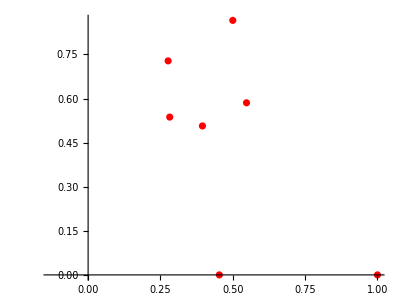

```mathematica
ComplexListPlot[Flatten[c],PlotStyle->Red]
```

```mathematica
d=Table[Max[Abs[a[[i]]]],{i,Length[a]}]
```

{1.,1.,1.32472,1.55603,1.30408,1.48512,1.24741,2.08295}

```mathematica
e=Flatten[Table[If[Abs[a[[i,j]]]==d[[i]]&&Im[a[[i,j]]]>=0,a[[i,j]],Nothing],{i,Length[a]},{j,Length[a[[i]]]}]]
```

{1.,0.5+0.866025 ⅈ,-0.21508+1.30714 ⅈ,0.104877+1.55249 ⅈ,1.30408,-0.226699+1.46771 ⅈ,-0.547424+1.12087 ⅈ,2.08295}

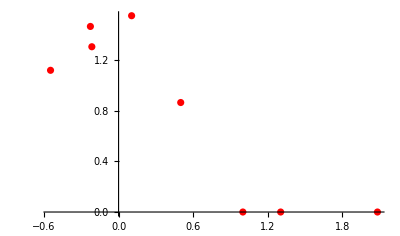

```mathematica
ComplexListPlot[Flatten[e],PlotStyle->Red]
```

```mathematica
q[x_]=ExpandAll[Product[p[x,i],{i,0,7}]]
```

Set::write: Tag List in {-1.+x,1.-1. x+x^2,1.+1.32472 x+1.32472 x^2+x^3,1.-1.36445 x+2.16576 x^2-1.36445 x^3+x^4,-1.+0.947513 x-1.40623 x^2+1.40623 x^3-0.947513 x^4+x^5,-1.+0.694706 x-0.694706 x^2+x^3,1.-0.488026 x+0.801309 x^2-0.488026 x^3+x^4,1.-1.05303 x+1.49479 x^2-1.58739 x^3+1.11992 x^4-1.9486 x^5+1.11992 x^6-1.58739 x^7+1.49479 x^8-1.05303 x^9+«1»}[x_] is Protected.

-1+7 x-27 x^2+73 x^3-148 x^4+234 x^5-254 x^6+69 x^7+531 x^8-1697 x^9+3446 x^10-5608 x^11+7874 x^12-9965 x^13+11541 x^14-12509 x^15+12748 x^16-12408 x^17+11518 x^18-10203 x^19+8643 x^20-6897 x^21+5232 x^22-3673 x^23+2418 x^24-1461 x^25+797 x^26-402 x^27+172 x^28-67 x^29+21 x^30-5 x^31+x^32

```mathematica
ComplexPlot[q[x],{x,-2-I*2,2+2*I},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100]
```

-Graphics-